```mathematica
loadNotebook["uproszczony_off_7_model.nb"];
model="psi";
loadNotebook["inz_off_model_"<>model<>".nb"];
```

```mathematica
wyrysuj[rozwiazanie_, tmax_,anim_,i_]:=Module[{},
loc="C:\\Users\\Admin\\Documents\\GitHub\\hog\\Magisterka\\doc - off\\";
pod={Subscript[θ, u1][t]->ArcTan[Sin[Subscript[θ, 1][t]]/(Cos[Subscript[θ, 1][t]]Sin[Subscript[ϕ, 1][t]])],Subscript[θ, u2][t]->ArcTan[Sin[Subscript[θ, 2][t]]/(Cos[Subscript[θ, 2][t]]Sin[Subscript[ϕ, 2][t]])]};
plot1=Plot[{(h[[1]]-hd[[1]]/.pod)/.rozwiazanie,(h[[2]]-hd[[2]]/.pod)/.rozwiazanie},{t,0,tmax},AxesLabel->{"t","e"},PlotLegends->Placed[{"e_x","e_y"},{0.90,0.75}],PlotRange->{-0.1,0.1}, PlotStyle->{Thick}];
plot1//Print;
Export[loc<>"inz_off_"<>model<>"_online_lin_"<>ToString[i]<>"_1.pdf",plot1];

plot2=Plot[{Subscript[θ, 0][t]-θd[t]/.rozwiazanie,Subscript[ψ, 1][t]-wirowanie*t/.rozwiazanie,Subscript[ψ, 1][t]-wirowanie*t/.rozwiazanie},{t,0,tmax},AxesLabel->{"t","e"},PlotLegends->Placed[{"e_θ_0","e_ψ_1","e_ψ_2"},{0.90,0.75}],PlotRange->{-0.1,0.1}, PlotStyle->{Thick}];
plot2//Print;
Export[loc<>"inz_off_"<>model<>"_online_lin_"<>ToString[i]<>"_2.pdf",plot2];

If[model=="psi",
plot3=Plot[{ster[[1]] /.rozwiazanie,ster[[4]] /.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","η-ϕ"},PlotLegends->Placed[{"η_1","η_4"},{0.90,0.75}],Axes->{True, True}];
plot3//Print;
Export[loc<>"inz_off_"<>model<>"_online_lin_"<>ToString[i]<>"_3.pdf",plot3];,

plot3=Plot[{ster[[1]] /.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","η-ϕ"},PlotLegends->Placed[{"η_1","η_4"},{0.90,0.75}],Axes->{True, True}];
plot3//Print;
Export[loc<>"inz_off_"<>model<>"_online_lin_"<>ToString[i]<>"_3.pdf",plot3];
];

If[model=="psi",
plot4=Plot[{ster[[2]] /.rozwiazanie,ster[[5]] /.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","η-θ"},PlotLegends->Placed[{"η_2","η_5"},{0.90,0.75}],Axes->{True, True}];
plot4//Print;
Export[loc<>"inz_off_"<>model<>"_online_lin_"<>ToString[i]<>"_4.pdf",plot4];,

plot4=Plot[{ster[[2]] /.rozwiazanie,ster[[4]] /.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","η-θ"},PlotLegends->Placed[{"η_2","η_4"},{0.90,0.75}],Axes->{True, True}];
plot4//Print;
Export[loc<>"inz_off_"<>model<>"_online_lin_"<>ToString[i]<>"_4.pdf",plot4];
];

plot5=Plot[{Subscript[ϕ, 1][t] /.rozwiazanie,Subscript[ϕ, 2][t] /.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","ϕ"},PlotLegends->Placed[{"ϕ_1","ϕ_2"},{0.90,0.75}],Axes->{True, True}];
plot5//Print;
Export[loc<>"inz_off_"<>model<>"_online_lin_"<>ToString[i]<>"_5.pdf",plot5];

plot6=Plot[{Subscript[θ, 1][t] /.rozwiazanie,Subscript[θ, 2][t] /.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","θ"},PlotLegends->Placed[{"θ_1","θ_2"},{0.90,0.75}],Axes->{True, True}];
plot6//Print;
Export[loc<>"inz_off_"<>model<>"_online_lin_"<>ToString[i]<>"_6.pdf",plot6];

plot7=Plot[{Subscript[ψ, 1]'[t] /.rozwiazanie,Subscript[ψ, 2]'[t] /.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","ψ̇"},PlotLegends->Placed[{"(ψ̇)_1","(ψ̇)_2"},{0.90,0.75}],Axes->{True, True}];
plot7//Print;
Export[loc<>"inz_off_"<>model<>"_online_lin_"<>ToString[i]<>"_7.pdf",plot7];

krzywa1[t_] = {x[t] ,y[t]} /. rozwiazanie;

p1[t_] = ((Agms[x[t], y[t], Subscript[θ, 0][t]]/.rozwiazanie).Transpose[{{0,0,0,1}}]) /. {l-> 0.1, R-> 0.03};
x1[t_] = (p1[t])[[1,1,1]];
y1[t_] = (p1[t])[[1,2,1]];
krzywas[t_] = {x1[t], y1[t]} /. rozwiazanie;

p2[t_] = ((Agm2[x[t], y[t], Subscript[θ, 0][t]]/.rozwiazanie).Transpose[{{0,0,0,1}}]) /. {l-> 0.1, R-> 0.03};
x2[t_] = (p2[t])[[1,1, 1]];
y2[t_] = (p2[t])[[1,2, 1]];
krzywa2[t_] = {x2[t], y2[t]}/. rozwiazanie;

ẋ[t_] = (x1'[t] /.rozwiazanie)[[1]];
ẏ[t_] = (y1'[t] /. rozwiazanie)[[1]];
v[t_] = Re[Sqrt[(ẋ[t])^2+(ẏ[t])^2]];
vd[t_] = Re[Sqrt[(xd'[t])^2+(yd'[t])^2]];

krzywad[t_]={xd[t],yd[t]};

a1 = Animate[
Show[
{Plot[v[t], {t, 0, tmax}, PlotRange->All,AxesLabel->{"t","v"}]},
{
Graphics[{PointSize[Large],Red,Point[Dynamic[{t,v[t]}]]}]
}
],{t,0,tmax}];

curvs = ParametricPlot[{krzywas[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->{Red}, Axes->{True, True}, AxesOrigin->{0,0}];
curv1 = ParametricPlot[{krzywa1[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Blue}, Axes->{True, True},AxesOrigin->{0,0}];
curv2 = ParametricPlot[{krzywa2[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Yellow}, Axes->{True, True}, AxesOrigin->{0,0}];
curvd = ParametricPlot[{krzywad[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Black}, Axes->{True, True}, AxesOrigin->{0,0}];plot8=ParametricPlot[{krzywa1[t],krzywad[t]},{t, 0, tmax},PlotRange->All,PlotStyle->{Red,Black}, Axes->{True, True}, AxesOrigin->{0,0}];
plot8//Print;
Export[loc<>"inz_off_"<>model<>"_online_lin_"<>ToString[i]<>"_8.pdf",plot8];


p11[t_]=Evaluate[{x[t],y[t]}/.rozwiazanie];
p22[t_]=Evaluate[{x2[t],y2[t]}/.rozwiazanie];
x11[t_]=(x[t]/.rozwiazanie)[[1]];
y11[t_]=(y[t]/.rozwiazanie)[[1]];
x22[t_]=(x2[t]/.rozwiazanie)[[1]];
y22[t_]=(y2[t]/.rozwiazanie)[[1]];
x33[t_]=(x[t]+0.2*Sin[θd[t]]/.rozwiazanie)[[1]];
y33[t_]=(y[t]-0.2*Cos[θd[t]]/.rozwiazanie)[[1]];
x44[t_]=(xd[t]+0.1(xd'[t]/vd[t])/.rozwiazanie)[[1]];
y44[t_]=(yd[t]+0.1(yd'[t]/vd[t])/.rozwiazanie)[[1]];
a2=Animate[
Show[
{curvs,curv1,curv2,curvd},
{
Graphics[{PointSize[0.03],Red,Point[Dynamic[p11[t]]]}],
Graphics[{PointSize[0.03], Red,Point[Dynamic[p22[t]]]}],
Graphics[{PointSize[0.02], Black,Point[Dynamic[{xd[t],yd[t]}]]}],
Graphics[
{Thickness[0.002],Green,
Line[
{
Dynamic[{x11[t],y11[t]}],
Dynamic[{x2[t],y2[t]}]
}
]
}],
Graphics[{Thickness[0.002],Black,Line[{Dynamic[{x11[t],y11[t]}],Dynamic[{x33[t],y33[t]}]}]}],
Graphics[{Thickness[0.005],Green,Line[{Dynamic[{xd[t],yd[t]}],Dynamic[{x44[t],y44[t]}]}]}]
}
],{t,0,tmax}];
If[anim,Print[a1],0];
If[anim,Print[a2],0];
0
];
```

```mathematica
wyliczSterowanie[wd_,w_,k1_]:=(
M= Inverse[D[w,{qu[t]}].G2u ];
Det[D[w,{qu[t]}].G2u ] // Simplify // Print;
K1=k1*IdentityMatrix[3];
K1[[3,3]]=5;
M=M.(D[wd,t]-K1.(w-wd));
AppendTo[M,M[[2]]*Sin[Subscript[θ, u1][t]]/Sin[Subscript[θ, u2][t]]];
M=M/.{Subscript[ϕ, u1][t]->Subscript[ψ, 1][t],Subscript[ϕ, u2][t]->Subscript[ψ, 2][t],Subscript[r, 1]->R*Sqrt[((Cos[Subscript[ϕ, 1][t]])^2)(Sin[Subscript[θ, 1][t]]^2 )+(Sin[Subscript[ϕ, 1][t]]^2 )],Subscript[r, 2]->R*Sqrt[((Cos[Subscript[ϕ, 2][t]])^2)(Sin[Subscript[θ, 2][t]]^2 )+(Sin[Subscript[ϕ, 2][t]]^2 )]};
(*M=M/.{Subscript[θ, u1][t]->ArcTan[-(Cos[Subscript[θ, 1][t]]Sin[Subscript[ϕ, 1][t]]),-Sin[Subscript[θ, 1][t]]],Subscript[θ, u2][t]->ArcTan[-(Cos[Subscript[θ, 2][t]]Sin[Subscript[ϕ, 2][t]]),-Sin[Subscript[θ, 2][t]]]};*)
(*M=M/.{Subscript[θ, u1][t]->ArcTan[Sin[Subscript[θ, 1][t]]/(Cos[Subscript[θ, 1][t]]Sin[Subscript[ϕ, 1][t]])],Subscript[θ, u2][t]->ArcTan[Sin[Subscript[θ, 2][t]]/(Cos[Subscript[θ, 2][t]]Sin[Subscript[ϕ, 2][t]])]};*)
M=M/.{Subscript[θ, u1][t]->ArcTan[Sin[Subscript[θ, 1][t]]/(Cos[Subscript[θ, 1][t]]Sin[Subscript[ϕ, 1][t]])],Subscript[θ, u2][t]->ArcTan[Sin[Subscript[θ, 2][t]]/(Cos[Subscript[θ, 2][t]]Sin[Subscript[ϕ, 2][t]])]};
M=M /.{l-> 0.1, R-> 0.03};
M
);
```

-0.15 r_1

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

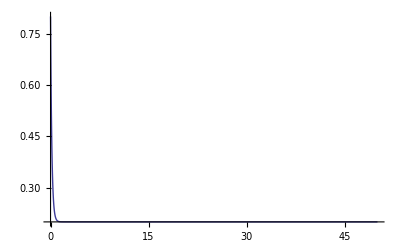

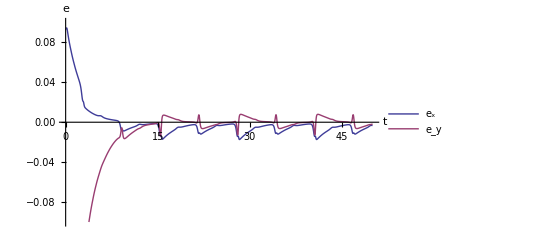

-Graphics-

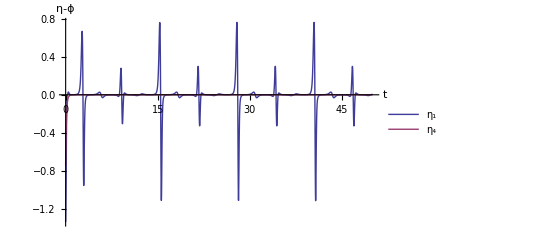

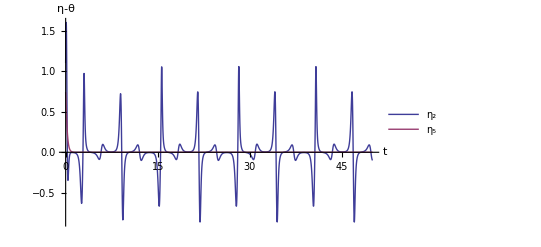

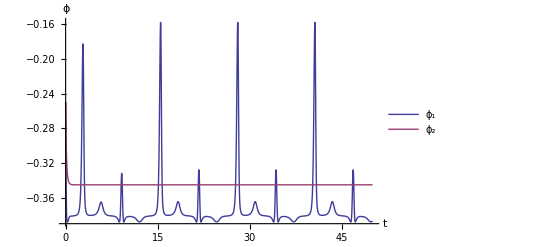

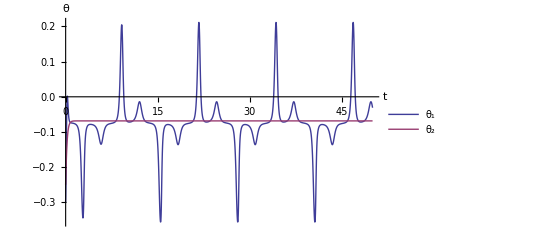

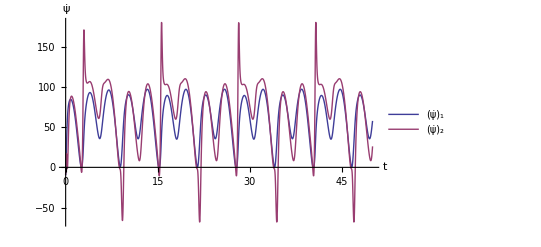

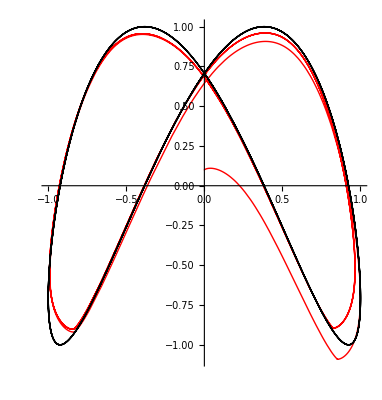

```mathematica
{xd[t_],yd[t_]}=osemka[t,1];
td[t_]=0.2;(*If[ArcTan[xd'[t],yd'[t]]>-Pi/2,ArcTan[xd'[t],yd'[t]],ArcTan[xd'[t],yd'[t]]+2Pi];*)
d = 0.15;
h={x[t]+d*Cos[Subscript[θ, u1][t]+Subscript[θ, 0][t]],y[t]+d*Sin[Subscript[θ, u1][t]+Subscript[θ, 0][t]],Subscript[θ, u2][t]};
hd={xd[t],yd[t],td[t]};
M =wyliczSterowanie[hd,h,0.4];

w1 = Solve[{0.02==0.03*Sqrt[((Cos[Subscript[ϕ, 1][t]])^2)(Sin[Subscript[θ, 1][t]]^2 )+(Sin[Subscript[ϕ, 1][t]]^2 )],  Tan[Subscript[θ, u1][t]] ==(Sin[Subscript[θ, 1][t]])/(Cos[Subscript[θ, 1][t]]Sin[Subscript[ϕ, 1][t]])}, {Subscript[ϕ, 1][t],Subscript[θ, 1][t]}];w2 = Solve[{0.02==0.03*Sqrt[((Cos[Subscript[ϕ, 2][t]])^2)(Sin[Subscript[θ, 2][t]]^2 )+(Sin[Subscript[ϕ, 2][t]]^2 )],  Tan[Subscript[θ, u2][t]] ==(Sin[Subscript[θ, 2][t]])/(Cos[Subscript[θ, 2][t]]Sin[Subscript[ϕ, 2][t]])}, {Subscript[ϕ, 2][t],Subscript[θ, 2][t]}];
ster={Subscript[ϕ, 1][t],Subscript[θ, 1][t],Subscript[ψ, 1][t], Subscript[ϕ, 2][t], Subscript[θ, 2][t],Subscript[ψ, 2][t]};
ster = ster /.{Subscript[ϕ, 1][t]->-1. ArcCos[trim[(√(9.-10000. r1[t]^2+9. Tan[Subscript[θ, u1][t]]^2-10000. r1[t]^2 Tan[Subscript[θ, u1][t]]^2))/(√(9.+9. Tan[Subscript[θ, u1][t]]^2-10000. r1[t]^2 Tan[Subscript[θ, u1][t]]^2)),-1, 1]],Subscript[θ, 1][t]->-1. ArcSin[trim[(100. r1[t] Tan[Subscript[θ, u1][t]])/(√(9.+9. Tan[Subscript[θ, u1][t]]^2)),-1, 1]]};
ster = ster /.{Subscript[ϕ, 2][t]->-1. ArcCos[trim[(√(9.-10000. r2[t]^2+9. Tan[Subscript[θ, u2][t]]^2-10000. r2[t]^2 Tan[Subscript[θ, u2][t]]^2))/(√(9.+9. Tan[Subscript[θ, u2][t]]^2-10000. r2[t]^2 Tan[Subscript[θ, u2][t]]^2)),-1,1]],Subscript[θ, 2][t]->-1. ArcSin[trim[(100. r2 [t]Tan[Subscript[θ, u2][t]])/(√(9.+9. Tan[Subscript[θ, u2][t]]^2)),-1,1]]};
(*ster=ster/.w2[[5]];*)
ster = ster /.{Subscript[ψ, 1][t]->Subscript[ϕ, u1][t],Subscript[ψ, 2][t]->Subscript[ϕ, u2][t]};
ster // MatrixForm;

wirowanie = 200;
ster=D[ster,t];
ster=ster/.{Subscript[ϕ, u1][t]->Subscript[ψ, 1][t],Subscript[ϕ, u2][t]->Subscript[ψ, 2][t]};
ster=ster/.{r1[t]->R*Sqrt[((Cos[Subscript[ϕ, 1][t]])^2)(Sin[Subscript[θ, 1][t]]^2 )+(Sin[Subscript[ϕ, 1][t]]^2 )],r2[t]->R*Sqrt[((Cos[Subscript[ϕ, 2][t]])^2)(Sin[Subscript[θ, 2][t]]^2 )+(Sin[Subscript[ϕ, 2][t]]^2 )]};
ster=ster/.{Subscript[θ, u1][t]->ArcTan[Sin[Subscript[θ, 1][t]]/(Cos[Subscript[θ, 1][t]]Sin[Subscript[ϕ, 1][t]])],Subscript[θ, u2][t]->ArcTan[Sin[Subscript[θ, 2][t]]/(Cos[Subscript[θ, 2][t]]Sin[Subscript[ϕ, 2][t]])]};
ster=ster/.{D[Subscript[θ, u1][t],t]->M[[1]],D[Subscript[ϕ, u1][t],t]->M[[2]],D[Subscript[θ, u2][t],t]->M[[3]],D[Subscript[ϕ, u2][t],t]->M[[4]],D[r1[t],t]->0.00*(M[[2]]-wirowanie),D[r2[t],t]->-0.0*(0.03*Sqrt[((Cos[Subscript[ϕ, 2][t]])^2)(Sin[Subscript[θ, 2][t]]^2 )+(Sin[Subscript[ϕ, 2][t]]^2 )]-0.005)};
ster //MatrixForm;
ster=ster/.{l-> 0.1, R-> 0.03};
q0={x[0]== 0, y[0]==0.1, Subscript[θ, 0][0]==0, Subscript[ϕ, 1][0]==-0.25, Subscript[θ, 1][0]== -0.3, Subscript[ψ, 1][0]==0,Subscript[ϕ, 2][0]== -0.25, Subscript[θ, 2][0]==-0.25, Subscript[ψ, 2][0]==0};

tmax =50;
pstrona = Transpose[G2.Transpose[{η[t]}]][[1]];
lstrona = D[q[t],t];
rownanie = Apply[Equal, Transpose[{lstrona, pstrona}],1];
tosolve=If[model=="psi",
(rownanie //.{Subscript[η, 1][t] -> ster[[1]], Subscript[η, 2][t]->ster[[2]],Subscript[η, 3][t]->ster[[3]],Subscript[η, 4][t]->ster[[4]],Subscript[η, 5][t]->ster[[5]], l-> 0.1, R-> 0.03}) ~Join~ q0,
(rownanie //.{Subscript[η, 1][t] -> ster[[1]], Subscript[η, 2][t]->ster[[2]],Subscript[η, 3][t]->ster[[3]],Subscript[η, 4][t]->ster[[5]],Subscript[η, 5][t]->ster[[6]], l-> 0.1, R-> 0.03}) ~Join~ q0
];
tosolve = tosolve~Join~{WhenEvent[Subscript[ϕ, 1][t]>-0.01 ,Subscript[ϕ, 1][t]->-0.02]};
roz = NDSolve[tosolve, {x,y, Subscript[θ, 0],Subscript[ϕ, 1], Subscript[θ, 1],Subscript[ψ, 1], Subscript[ϕ, 2], Subscript[θ, 2],Subscript[ψ, 2]}, {t,0,tmax}, Method->Automatic, MaxSteps->10000000];
(*Plot[0.03*Sqrt[((Cos[Subscript[ϕ, 1][t]])^2)(Sin[Subscript[θ, 1][t]]^2 )+(Sin[Subscript[ϕ, 1][t]]^2 )]/.roz,{t,0,tmax}];
Plot[0.03*Sqrt[((Cos[Subscript[ϕ, 2][t]])^2)(Sin[Subscript[θ, 2][t]]^2 )+(Sin[Subscript[ϕ, 2][t]]^2 )]/.roz,{t,0,tmax}]*)
Plot[ArcTan[Sin[Subscript[θ, 2][t]]/(Cos[Subscript[θ, 2][t]]Sin[Subscript[ϕ, 2][t]])]/.roz,{t,0,tmax}]
wyrysuj[roz,tmax, True,0];
```